```mathematica
plotUtils=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"plot_utils","plot_utils.m"}];
<<(plotUtils)
```

```mathematica
Conv[rule_]:=Module[{vars=rule/.Rule[a_,b_]->a},
Table[d[[n]]/.rule,{}]
]
```

```mathematica
(*BB*)
```

```mathematica
sequence=U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
sequenceS=U[-Δ1,Ω1].U[-Δ2,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];

(*error=0.01*)
rule1={Δ1->0.82801,Δ2->-0.01376,Ω1->0.6472};(*N=4, BW=0.4*)
rule2={Δ1->0.58082,Δ2->-0.3101,Δ3->-2.73308,Δ4->0.41314,Ω1->0.7501};(*N=4, BW=0.5*)

(*error=0.001*)
rule3={Δ1->0.02061,Δ2->-0.89784,Ω1->0.68257};(*N=4, BW=0.3*)
rule4={Δ1->0.54833,Δ2->0.04597,Δ3->-1.06142,Δ4->0.50126,Ω1->0.58714};(*N=4, BW=0.3*)

(*error=0.0001*)
rule5={Δ1->-0.9267,Δ2->0.0227,Ω1->0.6750};(*N=4, BW=-0.2, 0.23*)
rule6={Δ1->0.6465,Δ2->-0.0024,Δ3->-1.1049,Δ4->0.6265,Ω1->0.6197};(*N=4, BW=-0.21, 0.23*)

prob5=GetProbFn[sequenceS,rule5];
text5=text["X4",{0.7,0.55}];
prob6=GetProbFn[sequence,rule6];
text6=text["H4",{0.6,0.46}];
```

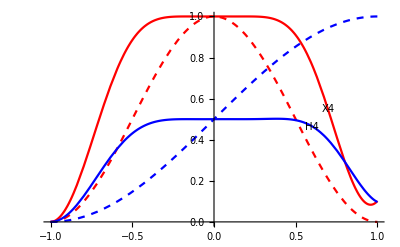

```mathematica
path=FileNameJoin[{NotebookDirectory[],"paper"}];
fname=FileNameJoin[{path,"BB.pdf"}];

pl=Plot[{single[1],single[1/2],prob5,prob6},{ϵ,-1,1},Epilog->{text5,text6},PlotStyle->{{Dashed,Red},{Dashed,Blue},Red,Blue}]
Export[fname,pl]
```

```mathematica
(*NB*)
```

```mathematica
sequence=U[Δ1,Ω1].U[Δ2,Ω1].U[Δ3,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];

(*error=0.01*)
rule1={Δ1->0.22208,Δ2->0.94196,Δ3->-0.00184,Δ4->2.4957,Ω1->0.64712};(*N=7, BW=0.5*)
rule2={Δ1->2.62761,Δ2->0.58969,Δ3->0.61251,Δ4->0.30148,Ω1->0.76082};(*N=7, BW=0.4*)

(*error=0.001*)
rule3={Δ1->6.67628,Δ2->-2.27954,Δ3->-1.60772,Δ4->6.52809,Ω1->-1.3548};(*N=7, BW=0.6*)
rule4={Δ1->0.39895,Δ2->0.79794,Δ3->0.70767,Δ4->-2.83593,Ω1->-0.64291};(*N=7, BW=0.6*)

(*error=0.0001*)
rule5={Δ1->0.7207,Δ2->-0.1269,Δ3->0.2682,Δ4->0.5699,Ω1->0.4036};(*N=7, BW=0.8(-0.2,0.22); area=2.83π*)
rule6={Δ1->2.7101,Δ2->0.6500,Δ3->0.7199,Δ4->0.3204,Ω1->0.7206};(*N=7, BW=0.7(-0.3,0.33); area=5.04π*)

prob5=GetProbFn[sequence,rule5];
text5=text["X7",{0.37,0.31}];
prob6=GetProbFn[sequence,rule6];
text6=text["H7",{0.17,0.31}];
```

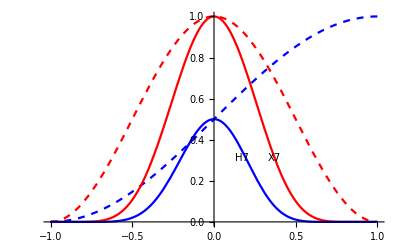

```mathematica
path=FileNameJoin[{NotebookDirectory[],"paper"}];
fname=FileNameJoin[{path,"NB.pdf"}];

pl=Plot[{single[1],single[1/2],prob5,prob6},{ϵ,-1,1},Epilog->{text5,text6},PlotStyle->{{Dashed,Red},{Dashed,Blue},Red,Blue}]
Export[fname,pl]
```

```mathematica
(*PB*)
```

```mathematica
sequence=U[Δ8,Ω1].U[Δ7,Ω1].U[Δ6,Ω1].U[Δ5,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];

(*error=0.01*)
rule1={Δ1->0.3847,Δ2->0.5165,Δ3->-2.4852,Δ4->0.549,Δ5->0.4073,Δ6->0.3837,Δ7->0.0138,Δ8->-0.8335,Ω1->0.6197};(*N=8, BW=0.2, area=4.96π*)
rule2={Δ1->2.6171,Δ2->0.5036,Δ3->0.2977,Δ4->0.1954,Δ5->0.8605,Δ6->-0.6183,Δ7->1.8844,Δ8->1.8191,Ω1->0.8250};(*N=8, BW=0.3, area=6.6π*)

prob1=GetProbFn[sequence,rule1];
text1=text["X8",{0.46,0.37}];
prob2=GetProbFn[sequence,rule2];
text2=text["H8",{0.47,0.70}];
```

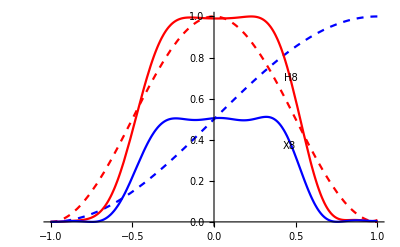

```mathematica
path=FileNameJoin[{NotebookDirectory[],"paper"}];
fname=FileNameJoin[{path,"PB.pdf"}];

pl=Plot[{single[1],single[1/2],prob1,prob2},{ϵ,-1,1},Epilog->{text1,text2},PlotStyle->{{Dashed,Red},{Dashed,Blue},Red,Blue}]
Export[fname,pl]
```